```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=β∈Reals&&Ω∈Reals&&t∈Reals&&β>0 && Ω>0 &&t>0&&β<π/4&&ωL∈Reals&& ωL>0&&A∈Reals&&A>0&&B∈Reals&&B>0&& m∈PositiveIntegers&&n∈PositiveIntegers&&k∈PositiveIntegers&&p0∈PositiveIntegers && l∈PositiveIntegers&&m0∈PositiveIntegers && m1∈PositiveIntegers&&n0∈PositiveIntegers && n1∈PositiveIntegers&&τg∈Reals&& τg>0&&Θ∈Reals&&τl∈Reals&& τl>0 && M∈PositiveIntegers &&ωl∈Reals&& ωl>0&&τu∈Reals&& τu>0;
```

```mathematica
Ucnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
```

```mathematica
(*first check should be if we get the correct dynamics with B=0 and with/without off-resonant drive*)
H0check=((ωL*Cos[β]-ω)*Cos[β]-Ω*Sin[β]*Cos[β]*Cos[ϕ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H1check=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2]/.{ω->ωL-A,Cos[β]->1,Sin[β]->0, ω1->ωL-A};
H0check //MatrixForm
H1check //MatrixForm
```

(A/2 | 1/2 Ω Cos[ϕ]-1/2 ⅈ Ω Sin[ϕ]
1/2 Ω Cos[ϕ]+1/2 ⅈ Ω Sin[ϕ] | -A/2)

(0 | 1/2 Ω Cos[ϕ]-1/2 ⅈ Ω Sin[ϕ]
1/2 Ω Cos[ϕ]+1/2 ⅈ Ω Sin[ϕ] | 0)

```mathematica
(*OK passt!!*)
```

```mathematica
(*now build time evolution operator including off-resonant driving and perpendicular component for both subspaces*)
```

```mathematica
(*Hamiltonian for both electronic subspaces in RF with RWA*)
```

```mathematica
H0=((ωL*Cos[β]-ω)*Cos[β]-Ω*Sin[β]*Cos[β]*Cos[ϕ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2];
H1=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2];
```

```mathematica
H0 //MatrixForm
H1 //MatrixForm
```

(1/2 (Cos[β] (-ω+ωL Cos[β])-Ω Cos[β] Cos[ϕ] Sin[β]) | 1/2 (Ω Cos[β]^2 Cos[ϕ]-ω Sin[β]+ωL Cos[β] Sin[β])-1/2 ⅈ Ω Cos[β] Sin[ϕ]
1/2 (Ω Cos[β]^2 Cos[ϕ]-ω Sin[β]+ωL Cos[β] Sin[β])+1/2 ⅈ Ω Cos[β] Sin[ϕ] | 1/2 (-Cos[β] (-ω+ωL Cos[β])+Ω Cos[β] Cos[ϕ] Sin[β]))

(1/2 ((-ω+ω1) Cos[β]-Ω Cos[β] Cos[ϕ] Sin[β]) | 1/2 (Ω Cos[β]^2 Cos[ϕ]+(-ω+ω1) Sin[β])-1/2 ⅈ Ω Cos[β] Sin[ϕ]
1/2 (Ω Cos[β]^2 Cos[ϕ]+(-ω+ω1) Sin[β])+1/2 ⅈ Ω Cos[β] Sin[ϕ] | 1/2 (-((-ω+ω1) Cos[β])+Ω Cos[β] Cos[ϕ] Sin[β]))

```mathematica
U0=MatrixExp[-ⅈ*H0*t];
U1 = MatrixExp[-ⅈ*H1*t];
```

```mathematica
(*I could not run this test because the evalution took too long:*)
Transpose[Conjugate[U0]].U0//ComplexExpand//Simplify//MatrixForm
```

```mathematica
Transpose[Conjugate[U1]].U1//ComplexExpand//Simplify//MatrixForm
```

```mathematica
(*first check sequence for a CNOT on nuclear spin without dynamical decoupling sequences. For this, ϕ->0*)
```

```mathematica
See if I can find conditions such that the static magnetic field may remain unchanged
```

```mathematica
(*build time evolution operator, plug in condition for driving frequency ω and phase ϕ. First see if we can achieve a CNOT without DD sequences, thus we put ϕ->0*)
H0s=H0/.{ϕ->0,ω->-Ω*Sin[β]+ω1}//FullSimplify;
H1s=H1/.{ϕ->0,(ω1-ω)->Ω*Sin[β]}//FullSimplify; 
H0s//MatrixForm
H1s//MatrixForm
H0s1=H0/.{ϕ->π,ω->Ω*Sin[β]-ω1}//FullSimplify;
H1s1=H1/.{ϕ->π,(ω1-ω)->-Ω*Sin[β]}//FullSimplify; 
H0s1//MatrixForm
H1s1//MatrixForm
```

(1/2 Cos[β] (-ω1+ωL Cos[β]) | 1/2 (Ω-ω1 Sin[β]+ωL Cos[β] Sin[β])
1/2 (Ω-ω1 Sin[β]+ωL Cos[β] Sin[β]) | 1/2 Cos[β] (ω1-ωL Cos[β]))

(0 | Ω/2
Ω/2 | 0)

(1/2 Cos[β] (ω1+ωL Cos[β]) | 1/2 (-Ω+(ω1+ωL Cos[β]) Sin[β])
1/2 (-Ω+(ω1+ωL Cos[β]) Sin[β]) | -1/2 Cos[β] (ω1+ωL Cos[β]))

(0 | -Ω/2
-Ω/2 | 0)

```mathematica
(*Rabi drive in both subspaces*)
Ω0g=Sqrt[(1/2 Cos[β] (-ω1+ωL Cos[β]))^2+(1/2 (Ω-ω1 Sin[β]+ωL Cos[β] Sin[β]))^2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]}//FullSimplify;
Ω0u=Sqrt[(1/2 Cos[β] (ω1+ωL Cos[β]))^2+(1/2 (-Ω+(ω1+ωL Cos[β]) Sin[β]))^2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]}//FullSimplify;
```

```mathematica
(*condition for gate time, but this time, eliminate driving strength. Also introduce rotation angle Θ for the CROT gate.*)
Ωg=Θg/(M*τg);
Ωu=Θu/(M*τu);
```

```mathematica
(*Condition for gate time for a NOT in the 1-subspace. We allow for different driving strengths and different integer parameters characterizing the rotations of the bloch vector, but the static external field and thus the Larmor frequency is supposed to be the same*)
Ω0g=√(Ω^2+((A^2+B^2-A ωL) (A^2+B (B-2 Ω)-A ωL))/(B^2+(A-ωL)^2))/.{Ω->Ωg}
Ω0u=1/2 √(A^2-4 B Ω+Ω^2-4 A ωL+4 ωL^2+(B (A^2+B^2) (B+2 Ω)-2 A B (B+Ω) ωL)/(B^2+(A-ωL)^2))/.{Ω->Ωu}
```

√(Θg^2/(M^2 τg^2)+((A^2+B^2-A ωL) (A^2+B (B-(2 Θg)/(M τg))-A ωL))/(B^2+(A-ωL)^2))

1/2 √(A^2+Θu^2/(M^2 τu^2)-(4 B Θu)/(M τu)-4 A ωL+4 ωL^2+(B (A^2+B^2) (B+(2 Θu)/(M τu))-2 A B (B+Θu/(M τu)) ωL)/(B^2+(A-ωL)^2))

```mathematica
condg=FullSimplify[Ω0g^2*τg^2/(π^2*m0^2)]
condu=FullSimplify[Ω0u^2*τu^2/(π^2*m1^2)]
```

(τg^2 (Θg^2/(M^2 τg^2)+((A^2+B^2-A ωL) (A^2+B (B-(2 Θg)/(M τg))-A ωL))/(B^2+(A-ωL)^2)))/(m0^2 π^2)

(τu^2 (A^2+(Θu (Θu-4 B M τu))/(M^2 τu^2)-4 A ωL+4 ωL^2+(B (A^2+B^2) (2 Θu+B M τu)-2 A B (Θu+B M τu) ωL)/(M τu (B^2+(A-ωL)^2))))/(4 m1^2 π^2)

```mathematica
condgt=condg/.{ωL->2*π/τl, τg->k*τl}//FullSimplify
condut=condu/.{ωL->2*π/τl, τu->l*τl}//FullSimplify
```

(Θg^2+(k M τl^2 (-2 A π+(A^2+B^2) τl) (-2 (A k M π+B Θg)+(A^2+B^2) k M τl))/(4 π^2-4 A π τl+(A^2+B^2) τl^2))/(M^2 m0^2 π^2)

(l^2 τl^2 (A^2+(16 π^2)/τl^2-(8 A π)/τl+(Θu (Θu-4 B l M τl))/(l^2 M^2 τl^2)+(-(4 A B π (Θu+B l M τl))/τl+B (A^2+B^2) (2 Θu+B l M τl))/(l M (B^2+(A-(2 π)/τl)^2) τl)))/(4 m1^2 π^2)

```mathematica
N[Solve[condgt==1/.{A->190,B->10,m0->20,M->4,τl->0.04208460399494908,k->8},Θg]]
```

{{Θg→1.5708},{Θg→118.538}}

```mathematica
val=-1.5707963267948966;
N[Solve[condgt==1/.{A->190,B->10,m0->20,M->8,Θg->(1.5707963267948966+val),k->8},τl]]
N[Solve[condut==1/.{A->190,B->10,m1->20,M->4,Θu->(3.141592653589793-(1.5707963267948966-val)),l->8},τl]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{τl→0.0420314}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{τl→0.148472}}

```mathematica
Θg/(M*τg)/.{Θg->π/2,M->4,τg->8*0.04208460399494908}
```

1.1664

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{τl→0.148491}}

```mathematica
N[π]
```

3.14159

```mathematica
Solve[condut==1,Θu, Assumptions->A∈Reals&&B∈Reals&&B>0&&A>0&&k∈PositiveIntegers&&l∈PositiveIntegers&&m0∈PositiveIntegers && m1∈PositiveIntegers&&τl∈Reals&& τl>0 && M∈PositiveIntegers]//FullSimplify
```

```mathematica
Solve[condu==1,Θ]
```

```mathematica
try the same with a resonant drive
```

```mathematica
H0t=H0/.{ϕ->0,ω->Sqrt[B^2+(ωL-A)^2],ω1->Sqrt[B^2+(ωL-A)^2]}//FullSimplify;
H1t=H1/.{ϕ->0,ω->Sqrt[B^2+(ωL-A)^2],ω1->Sqrt[B^2+(ωL-A)^2]}//FullSimplify; 
H0t//MatrixForm
H1t//MatrixForm
U1t = MatrixExp[-ⅈ*H1t*tg]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2]}//FullSimplify;
U0t = MatrixExp[-ⅈ*H0t*tg]//TrigExpand;
U0t=U0t/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2]};
U1t//MatrixForm;
U0t//MatrixForm;
```

(1/2 Cos[β] (-√(B^2+(A-ωL)^2)+ωL Cos[β]-Ω Sin[β]) | 1/2 (Ω Cos[β]^2-√(B^2+(A-ωL)^2) Sin[β]+ωL Cos[β] Sin[β])
1/2 (Ω Cos[β]^2-√(B^2+(A-ωL)^2) Sin[β]+ωL Cos[β] Sin[β]) | 1/2 Cos[β] (√(B^2+(A-ωL)^2)-ωL Cos[β]+Ω Sin[β]))

(-1/2 Ω Cos[β] Sin[β] | 1/2 Ω Cos[β]^2
1/2 Ω Cos[β]^2 | 1/2 Ω Cos[β] Sin[β])

```mathematica
(*try to find a solution for both conditions for Ω. No, wait. In the above matrix, the magnitude of the z-component only depends on the angle β*)
```

```mathematica
c11=1/2 Ω Cos[β] Sin[β]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2]}//FullSimplify;(*this is not solvable as we cannot tune β only trivial solution for Ω=0 exists*)
(*zero-subspace needs to be prop. to identity:*)
Ω0t=Sqrt[(1/2 Cos[β] (-√(B^2+(A-ωL)^2)+ωL Cos[β]-Ω Sin[β]))^2+(1/2 (Ω Cos[β]^2-√(B^2+(A-ωL)^2) Sin[β]+ωL Cos[β] Sin[β]))^2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]}//FullSimplify
```

1/2 √(A^2+Ω^2+(B^2 (A^2+B^2-Ω^2-2 A ωL))/(B^2+(A-ωL)^2))

```mathematica
test=Solve[Ω0t^2*tg^2==π^2*m^2/.{A->200,B->200,ωL->980,n->0,m->1},Ω][[2]][[1]][[2]][[1]];
N[U1t] /.{A->200,B->200,ωL->980,Ω->test,n->0}//MatrixForm
N[U0t] /.{ A->200,B->200,ωL->980,Ω->test,n->0}//MatrixForm
N[U0s] /.{A->200,B->0,ωL->980,Ω->test,n->0}//MatrixForm;
(*also: der Fehler im 1-Unterraum entsteht durch eine zustätzliche z-Rotation. Und diese Komponente wird mit der Wahl der synchronisierten Stärke des Treibens und der Gatterzeit klein.*)
ω1=N[Sqrt[B^2+(ωL-A)^2]/.{A->200,B->200,ωL->980}];
sinbeta=N[B/Sqrt[B^2+(ωL-A)^2]/.{A->200,B->200,ωL->400}];
cosbeta=N[(ωL-A)/Sqrt[B^2+(ωL-A)^2]/.{A->200,B->200,ωL->400}];
(*Beachte: das Dreieck wird von der senkrechten Komponente und von A-wl aufgespannt!!!*)
(*Das heißt die Frage ist ob die Synchronisierung auch den 0 unterraum synchronisiert.*)
```

(0.0492028+0.248075 ⅈ | 0.-0.967491 ⅈ
0.-0.967491 ⅈ | 0.0492028-0.248075 ⅈ)

(0.5 2.71828^((0.-0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963))+0.5 2.71828^((0.+0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963))+0.00156137 2.71828^((0.-0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963)-0.00156137 2.71828^((0.+0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963) | 0.00147394 2.71828^((0.-0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963)-0.00147394 2.71828^((0.+0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963)
0.00147394 2.71828^((0.-0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963)-0.00147394 2.71828^((0.+0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963) | 0.5 2.71828^((0.-0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963))+0.5 2.71828^((0.+0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963))-0.00156137 2.71828^((0.-0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963)+0.00156137 2.71828^((0.+0.0134912 ⅈ) √(-793622.+(4800105200 Cos[2. β])/4963)) √(-793622.+(4800105200 Cos[2. β])/4963))

(-1.-2.91713×10^-16 ⅈ | 0.+1.35446×10^-16 ⅈ
0.+1.35446×10^-16 ⅈ | -1.+2.91713×10^-16 ⅈ)

```mathematica
Now check correctness of solution with off-resonant drive
```

```mathematica
(*Replace angles with expressions for the hyperfine tensor components*)
H0s=FullSimplify[H0s]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]}
H1s = FullSimplify[H1s]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]}
(*and build time evolution operator for both subspaces*)
U0s=MatrixExp[-ⅈ*H0s*t];
U1s = MatrixExp[-ⅈ*H1s*t];
```

{{((-A+ωL) ((ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))-√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)),1/2 (-B+Ω+(B ωL (-A+ωL))/(B^2+(-A+ωL)^2))},{1/2 (-B+Ω+(B ωL (-A+ωL))/(B^2+(-A+ωL)^2)),((-A+ωL) (-(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2))}}

{{0,Ω/2},{Ω/2,0}}

```mathematica
Transpose[Conjugate[U0s]].U0s//FullSimplify//MatrixForm
```

```mathematica
Transpose[Conjugate[U1s]].U1s//FullSimplify//MatrixForm
```

```mathematica
(*Check analytical solution: Get condition for gate time for a NOT in the 1-subspace and plug it in the time evolution operator*)
```

```mathematica
Solve[U1s=={{0,-ⅈ},{-ⅈ,0}},t]
```

{{t→ConditionalExpression[-(-π-4 π C[1])/Ω, C[1]∈ℤ&&C[1]≥0]}}

```mathematica
(*Check: plug in conditions for gate time and driving strength. Works.*)
U0s=MatrixExp[-ⅈ*H0s*t]/.{t->(π*(2n+1))/Ω,A->200,B->20,ωL->430,n->0,m->1};
U0s=N[U0s]/.{Ω->1/533 (3040-1520 √1603),n->0};
U1s = MatrixExp[-ⅈ*H1s*t]/.t->(π*(2n+1))/Ω/.n->0//FullSimplify;
U0s//MatrixForm
U1s//MatrixForm
```

(-1.-2.91713×10^-16 ⅈ | 0.+1.35446×10^-16 ⅈ
0.+1.35446×10^-16 ⅈ | -1.+2.91713×10^-16 ⅈ)

(0 | -ⅈ
-ⅈ | 0)

```mathematica
(*OK superb.*)
```

```mathematica
(*Now include ϕ for DDrf sequence. Thus ϕ differs for odd and even pulses. Even pulses affect the dynamics of V0, odd of V1. ϕ -> 0 for k even and ϕ -> π for k odd. The condition for the detuning also depends on ϕ.*)
```

```mathematica
H0p0=H0/.{ϕ->0,ω->-Ω*Sin[β]+ω1}//FullSimplify;
H1p0=H1/.{ϕ->0,(ω1-ω)->Ω*Sin[β]}//FullSimplify; 
H0p1=H0/.{ϕ->π,ω->Ω*Sin[β]+ω1}//FullSimplify//TrigExpand;
H1p1=H1/.{ϕ->π,(ω1-ω)->-Ω*Sin[β]}//FullSimplify; 
H0p0//MatrixForm
H1p0//MatrixForm
H0p1//MatrixForm
H1p1//MatrixForm
```

(1/2 Cos[β] (-ω1+ωL Cos[β]) | 1/2 (Ω-ω1 Sin[β]+ωL Cos[β] Sin[β])
1/2 (Ω-ω1 Sin[β]+ωL Cos[β] Sin[β]) | 1/2 Cos[β] (ω1-ωL Cos[β]))

(0 | Ω/2
Ω/2 | 0)

(-1/2 ω1 Cos[β]+1/2 ωL Cos[β]^2 | -Ω/2-1/2 ω1 Sin[β]+1/2 ωL Cos[β] Sin[β]
-Ω/2-1/2 ω1 Sin[β]+1/2 ωL Cos[β] Sin[β] | 1/2 ω1 Cos[β]-1/2 ωL Cos[β]^2)

(0 | -Ω/2
-Ω/2 | 0)

```mathematica
(*Now the synchronization condition has to hold for the interpulse spacing τ. Thus the condition for the gate time is:*)
τ=(π*(2*n+1))/(2*M*Ω)
```

((1+2 n) π)/(2 M Ω)

```mathematica
(*condition for U0 depends on parity of pulse sequence*)
Ω0p0=Sqrt[(1/2 Cos[β] (-ω1+ωL Cos[β]))^2+(1/2 (Ω-ω1 Sin[β]+ωL Cos[β] Sin[β]))^2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
Ω0p1=Sqrt[(-1/2 ω1 Cos[β]+1/2 ωL Cos[β]^2)^2+(-Ω/2-1/2 ω1 Sin[β]+1/2 ωL Cos[β] Sin[β])^2]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
```

```mathematica
(*plug in condition for gate time*)
N[Solve[Ω0p0^2*τ^2==π^2*m^2,Ω]/.{A->190,B->10,ωL->430,n->0,m->1,M->8}]
N[Solve[Ω0p1^2*τ^2==π^2*m^2,Ω]/.{A->190,B->10,ωL->430,n->0,m->1,M->8}]
(*So the values for Ω differ with respect to the parity of the pulses*)
```

{{Ω→Undefined},{Ω→Undefined},{Ω→Undefined},{Ω→Undefined},{Ω→Undefined},{Ω→Undefined},{Ω→6.48774}}

{{Ω→Undefined},{Ω→Undefined},{Ω→Undefined},{Ω→Undefined},{Ω→6.33357}}

```mathematica
(*get realistic values for the frequency of the driving field and compare to ω1*)
(*Achtung, die hängen wiederum von der Rabi Frequenz ab, die dann auch von der Parität abhängt!*)
ω1=N[Sqrt[B^2+(ωL-A)^2]/.{A->190,B->10,ωL->430}]
ωp0=-Ω*Sin[β]+ω1/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]}/.{A->190,B->10,ωL->430,n->0,m->1,M->8,Ω->6.487739821580268}
ωp1=Ω*Sin[β]+ω1/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]}/.{A->190,B->10,ωL->430,n->0,m->1,M->8,Ω->6.333573345504025}
```

240.208

237.507

242.845

```mathematica
(*Also das funktioniert. Ein Skript für die besten Werte müsste ich noch schreiben. Aber zunächst sollte ich die Qualität der RWA überprüfen.*)
```

```mathematica
(*now look at DD sequence, thus include ϕ*)
H0=((ωL*Cos[β]-ω)*Cos[β]-Ω*Sin[β]*Cos[β]*Cos[ϕ])/2*PauliMatrix[3]+(-ω*Sin[β]+ωL*Cos[β]*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2];
H1=((ω1-ω)*Cos[β]-Ω*Cos[β]*Sin[β]*Cos[ϕ])/2*PauliMatrix[3]+((ω1-ω)*Sin[β]+Ω*(Cos[β])^2*Cos[ϕ])/2*PauliMatrix[1]+(Ω*Cos[β]*Sin[ϕ])/2*PauliMatrix[2];
H0=H0/.{ω->-Ω*Sin[β]+ω1}//FullSimplify;
H1=H1/.{(ω1-ω)->Ω*Sin[β]}//FullSimplify; 
H0 //MatrixForm
H1 //MatrixForm
```

ω→-(B^2 Ω)/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)

(1/2 Cos[β] (-ω1+ωL Cos[β]+(Ω-Ω Cos[ϕ]) Sin[β]) | 1/2 (Ω Cos[β]^2 Cos[ϕ]+Sin[β] (-ω1+Ω Sin[β])+Cos[β] (ωL Sin[β]-ⅈ Ω Sin[ϕ]))
1/2 (Ω Cos[β]^2 Cos[ϕ]+Sin[β] (-ω1+Ω Sin[β])+Cos[β] (ωL Sin[β]+ⅈ Ω Sin[ϕ])) | 1/2 Cos[β] (ω1-ωL Cos[β]+Ω (-1+Cos[ϕ]) Sin[β]))

(Ω Cos[β] Sin[β] Sin[ϕ/2]^2 | 1/2 Ω (Cos[β]^2 Cos[ϕ]+Sin[β]^2-ⅈ Cos[β] Sin[ϕ])
1/2 Ω (Cos[β]^2 Cos[ϕ]+Sin[β]^2+ⅈ Cos[β] Sin[ϕ]) | -Ω Cos[β] Sin[β] Sin[ϕ/2]^2)

```mathematica
H0=FullSimplify[H0]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H1 = FullSimplify[H1]/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
```

```mathematica
(*get condition for unitaries for both subspaces*)
```

```mathematica
(*condition for gate time in terms of hyperfine components A and B and nuclear larmor frequency ωL*)
```

```mathematica
tg=(k*π)/(Ω* (Cos[β]^2-Sin[β]^2))/.{Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2]}
```

(k π)/(Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)))

```mathematica
U0s=MatrixExp[-ⅈ*H0s1*t]/.t->(k π)/(Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)));
```

```mathematica
(*plug in condition for synchronization in units of MHz*)
```

```mathematica
U0sync=U0s/.{A->190,B->10,ωL->430,k->1,Ω->92.5058680008477}
```

{{-1.+3.38869×10^-15 ⅈ,0.-5.32352×10^-16 ⅈ},{0.-5.32352×10^-16 ⅈ,-1.-3.38869×10^-15 ⅈ}}

```mathematica
(*So this works, this means that we can use this protocol for a conditional drive on the nuclear spin without decoupling sequences*)
```

```mathematica
(*This was the attempt to get the idenitiy analytically, but it took ages and I interrupted it*)
```

```mathematica
U0s/.{m->1,k->1,Ω->(A^2 B^6+B^8+A^3 B^2 ωL-2 A B^6 ωL-3 A^2 B^2 ωL^2+B^6 ωL^2+3 A B^2 ωL^3-B^2 ωL^4)/(3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4)-(√(3 A^10+6 A^8 B^2+3 A^6 B^4-4 A^8 B^4-8 A^6 B^6-4 A^4 B^8-4 A^6 B^8-8 A^4 B^10-4 A^2 B^12+4 A^4 B^12+8 A^2 B^14+4 B^16-24 A^9 ωL-42 A^7 B^2 ωL-18 A^5 B^4 ωL+18 A^7 B^4 ωL+34 A^5 B^6 ωL+16 A^3 B^8 ωL+32 A^5 B^8 ωL+40 A^3 B^10 ωL+8 A B^12 ωL-16 A^3 B^12 ωL-16 A B^14 ωL+84 A^8 ωL^2+126 A^6 B^2 ωL^2+45 A^4 B^4 ωL^2-20 A^6 B^4 ωL^2-50 A^4 B^6 ωL^2-24 A^2 B^8 ωL^2-97 A^4 B^8 ωL^2-72 A^2 B^10 ωL^2-4 B^12 ωL^2+24 A^2 B^12 ωL^2+8 B^14 ωL^2-168 A^7 ωL^3-210 A^5 B^2 ωL^3-60 A^3 B^4 ωL^3-34 A^5 B^4 ωL^3+20 A^3 B^6 ωL^3+16 A B^8 ωL^3+148 A^3 B^8 ωL^3+56 A B^10 ωL^3-16 A B^12 ωL^3+210 A^6 ωL^4+210 A^4 B^2 ωL^4+45 A^2 B^4 ωL^4+120 A^4 B^4 ωL^4+20 A^2 B^6 ωL^4-4 B^8 ωL^4-122 A^2 B^8 ωL^4-16 B^10 ωL^4+4 B^12 ωL^4-168 A^5 ωL^5-126 A^3 B^2 ωL^5-18 A B^4 ωL^5-146 A^3 B^4 ωL^5-22 A B^6 ωL^5+52 A B^8 ωL^5+84 A^4 ωL^6+42 A^2 B^2 ωL^6+3 B^4 ωL^6+92 A^2 B^4 ωL^6+6 B^6 ωL^6-9 B^8 ωL^6-24 A^3 ωL^7-6 A B^2 ωL^7-30 A B^4 ωL^7+3 A^2 ωL^8+4 B^4 ωL^8))/Abs[3 A^4-7 A^2 B^4+3 B^8-12 A^3 ωL+14 A B^4 ωL+18 A^2 ωL^2-7 B^4 ωL^2-12 A ωL^3+3 ωL^4]}//FullSimplify
```

```mathematica
(*now evaluate Fidelity including off-resonant drive and errors*)
(*First check Fidelity of synchronized process*)
```

```mathematica
VORs=KroneckerProduct[{{1,0},{0,0}},U0sync]+KroneckerProduct[{{0,0},{0,1}},U1s];
VORs//MatrixForm
```

(-1.+3.38869×10^-15 ⅈ | 0.-5.32352×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.-5.32352×10^-16 ⅈ | -1.-3.38869×10^-15 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.-1. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.-1. ⅈ | 0.+0. ⅈ)

```mathematica
Rz1=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, ⅈ, 0}, {0, 0, 0, ⅈ}});
Rz2=({{((-1)^k), 0, 0, 0}, {0, ((-1)^k), 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
Vcnots= Rz1.Rz2.VORs/. k->1
```

{{1.-3.38869×10^-15 ⅈ,0.+5.32352×10^-16 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+5.32352×10^-16 ⅈ,1.+3.38869×10^-15 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ}}

```mathematica
Ucnot=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
```

```mathematica
Favs=(Abs[Tr[Ucnot.Vcnots]]^2+4)/20//FullSimplify//ComplexExpand
```

1.

```mathematica
(*Now evaluate Fidelity of erraneous process*)
```

```mathematica
U0sOmega=U0s/.{A->190,B->10,ωL->430,k->1};
VOR=KroneckerProduct[{{1,0},{0,0}},U0sOmega]+KroneckerProduct[{{0,0},{0,1}},U1s];
VOR//MatrixForm;
Vcnot= Rz1.Rz2.VOR/. k->1;
```

```mathematica
Fav=(Abs[Tr[Ucnot.Vcnot]]^2+4)/20//FullSimplify//ComplexExpand;
```

```mathematica
Plot[{Fav},{Ω,0,200},Frame->True]
```

```mathematica
{"drawing.pdf","drawing.png","drawing.svg","energylevels_scetch_new.pdf","energylevels_scetch_new.png","energylevels_scetch_new.svg","energylevels_scetch.svg","NVCenter.pdf","NVCenter.png","NVCenter_scetch.svg"}
```

```mathematica
(*now plot fidelity of Rz-corrected process of free evolution. The free evolution of the 0-electron subspace is now in the rotating frame of the 1-electron subspace.
It is the Hamiltonian H0 where Ω->0.*)
```

```mathematica
H0corr0 = H0/.{Ω->0,ω->Ω*Sin[β]+ω1,Cos[β]->(ωL-A)/Sqrt[B^2+(ωL-A)^2],Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0corr = H0corr0/.{Sin[β]->B/Sqrt[B^2+(ωL-A)^2], ω1->Sqrt[B^2+(ωL-A)^2]};
H0corr // MatrixForm
```

(((-A+ωL) (-(B^2 Ω)/(√(B^2+(-A+ωL)^2))+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))-√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)) | -(B^2 ((B^2 Ω)/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2))
-(B^2 ((B^2 Ω)/(√(B^2+(-A+ωL)^2))+√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)) | -((-A+ωL) (-(B^2 Ω)/(√(B^2+(-A+ωL)^2))+(ωL (-A+ωL))/(√(B^2+(-A+ωL)^2))-√(B^2+(-A+ωL)^2)))/(2 √(B^2+(-A+ωL)^2)))

```mathematica
U0corr=MatrixExp[-ⅈ*t* H0corr] /.t->(-k π)/(Ω (-B^4/(B^2+(-A+ωL)^2)+(-A+ωL)^2/(B^2+(-A+ωL)^2)));
U0corr//MatrixForm;
```

```mathematica
U0corr2=KroneckerProduct[{{1,0},{0,0}},U0corr]+KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]];
U0corr2//MatrixForm;
```

```mathematica
VOR=KroneckerProduct[{{1,0},{0,0}},U0s]+KroneckerProduct[{{0,0},{0,1}},U1s];
VOR//MatrixForm;
(*The "reverse" time evolution in U0corr2 corrects the phase shift of pi of the 1-subspace!*)
Vcnots1= U0corr2.Rz1.VOR/.{A->190,B->0,ωL->430,k->1};
```

```mathematica
Fav=(Abs[Tr[Ucnot.Vcnots1]]^2+4)/20;
```

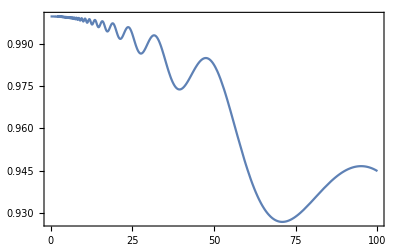

```mathematica
Plot[{Fav},{Ω,0,100},Frame->True]
```

```mathematica
(*now comupte fidelity of DDRF gate*)
```

{{(ⅇ^(-(ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(2 (B^2+(A-ωL)^2))) (-2 B^2 (-1+ⅇ^((ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(B^2+(A-ωL)^2))) (A-ωL) (-1+Cos[ϕ])+2 (1+ⅇ^((ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(B^2+(A-ωL)^2))) √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ])))/(2 √2 √(2 A^4+2 B^8-8 A^3 ωL+B^2 (1+3 B^2) ωL^2+2 ωL^4-2 A ωL (B^2+3 B^4+4 ωL^2)+A^2 (B^2+3 B^4+12 ωL^2)+B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ])),-((ⅇ^(-(ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(2 (B^2+(A-ωL)^2))) (-1+ⅇ^((ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(B^2+(A-ωL)^2))) (B^4 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[ϕ]+ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[ϕ]))/(√2 √((B^2+(A-ωL)^2) (2 A^4+2 B^8-8 A^3 ωL+B^2 (1+3 B^2) ωL^2+2 ωL^4-2 A ωL (B^2+3 B^4+4 ωL^2)+A^2 (B^2+3 B^4+12 ωL^2)+B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))))},{-((ⅇ^(-(ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(2 (B^2+(A-ωL)^2))) (-1+ⅇ^((ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(B^2+(A-ωL)^2))) (B^4 √(B^2+(A-ωL)^2)+√(B^2+(A-ωL)^2) (A-ωL)^2 Cos[ϕ]-ⅈ (B^2+(A-ωL)^2) (A-ωL) Sin[ϕ]))/(√2 √((B^2+(A-ωL)^2) (2 A^4+2 B^8-8 A^3 ωL+B^2 (1+3 B^2) ωL^2+2 ωL^4-2 A ωL (B^2+3 B^4+4 ωL^2)+A^2 (B^2+3 B^4+12 ωL^2)+B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ])))),(ⅇ^(-(ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(2 (B^2+(A-ωL)^2))) (2 B^2 (-1+ⅇ^((ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(B^2+(A-ωL)^2))) (A-ωL) (-1+Cos[ϕ])+2 (1+ⅇ^((ⅈ t Ω √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))/(B^2+(A-ωL)^2))) √(A^4+B^8-4 A^3 ωL+1/2 B^2 (1+3 B^2) ωL^2+ωL^4-A ωL (B^2+3 B^4+4 ωL^2)+1/2 A^2 (B^2+3 B^4+12 ωL^2)+1/2 B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ])))/(2 √2 √(2 A^4+2 B^8-8 A^3 ωL+B^2 (1+3 B^2) ωL^2+2 ωL^4-2 A ωL (B^2+3 B^4+4 ωL^2)+A^2 (B^2+3 B^4+12 ωL^2)+B^2 (-1+B^2) (A-ωL)^2 Cos[2 ϕ]))}}